```mathematica
OutForm[num_?NumericQ,width_Integer,ndig_Integer,OptionsPattern[]]:=Module[{mant,exp,val},{mant,exp}=MantissaExponent[num];
mant=ToString[NumberForm[mant,{ndig,ndig}]];
exp=If[Sign[exp]==-1,"-","+"]<>IntegerString[exp,10,2];
val=mant<>"E"<>exp;
StringJoin@PadLeft[Characters[val],width," "]];

ReadCube[cubeFileName_?StringQ]:=Module[{moltxt,nAtoms,lowerCorner,nx,ny,nz,xstep,ystep,zstep,atoms,desc1,desc2,xyzText,cubeDat,xgrid,ygrid,zgrid,dummy1,dummy2,atomicNumber,atomx,atomy,atomz,tmpString,headerTxt,bohr2angstrom},bohr2angstrom=1 (* 0.529177249 *) ;
moltxt=OpenRead[cubeFileName];
desc1=Read[moltxt,String];
desc2=Read[moltxt,String];
lowerCorner={0,0,0};
{nAtoms,lowerCorner[[1]],lowerCorner[[2]],lowerCorner[[3]]}=Read[moltxt,String]//ImportString[#,"Table"][[1]]&;
xyzText=ToString[nAtoms]<>"\n";
xyzText=xyzText<>desc1<>desc2<>"\n";
{nx,xstep,dummy1,dummy2}=Read[moltxt,String]//ImportString[#,"Table"][[1]]&;
{ny,dummy1,ystep,dummy2}=Read[moltxt,String]//ImportString[#,"Table"][[1]]&;
{nz,dummy1,dummy2,zstep}=Read[moltxt,String]//ImportString[#,"Table"][[1]]&;
Do[{atomicNumber,dummy1,atomx,atomy,atomz}=Read[moltxt,String]//ImportString[#,"Table"][[1]]&;
xyzText=If[Sign[lowerCorner[[1]]]==1,xyzText<>ElementData[atomicNumber,"Abbreviation"]<>OutForm[atomx,17,7]<>OutForm[atomy,17,7]<>OutForm[atomz,17,7]<>"\n",xyzText<>ElementData[atomicNumber,"Abbreviation"]<>OutForm[bohr2angstrom atomx,17,7]<>OutForm[bohr2angstrom atomy,17,7]<>OutForm[bohr2angstrom atomz,17,7]<>"\n"];,{nAtoms}];
cubeDat=Partition[Partition[ReadList[moltxt,Number,nx ny nz],nz],ny];
Close[moltxt];
moltxt=OpenRead[cubeFileName];
headerTxt=Read[moltxt,Table[String,{2+4+nAtoms}]];
Close[moltxt];
headerTxt=StringJoin@Riffle[headerTxt,"\n"];
xgrid=Range[lowerCorner[[1]],lowerCorner[[1]]+xstep (nx-1),xstep];
ygrid=Range[lowerCorner[[2]],lowerCorner[[2]]+ystep (ny-1),ystep];
zgrid=Range[lowerCorner[[3]],lowerCorner[[3]]+zstep (nz-1),zstep];
{cubeDat ,xgrid ,ygrid ,zgrid ,xyzText,headerTxt}];


CubePlot[{cub_,xg_,yg_,zg_,xyz_},count_,plotopts:OptionsPattern[]]:=Module[{xyzplot,bohr2picometer,datarange3D,pr},bohr2picometer=52.9177249;
datarange3D=bohr2picometer {{xg[[1]],xg[[-1]]},{yg[[1]],yg[[-1]]},{zg[[1]],zg[[-1]]}};
xyzplot=ImportString[xyz,"XYZ"];
Show[xyzplot,ListContourPlot3D[Transpose[cub,{3,2,1}],Evaluate[FilterRules[{plotopts},Options[ListContourPlot3D]]],Contours->{-count,count},ContourStyle->{Blue,Red},DataRange->datarange3D,MeshStyle->Gray,Lighting->{{"Ambient",White}}],Evaluate[FilterRules[{plotopts},{ViewPoint,ViewVertical,ImageSize}]]]];



WriteCube[cubeFileName_?StringQ,headerTxt_?StringQ,cubeData_]:=Module[{stream},stream=OpenWrite[cubeFileName,FormatType->FortranForm];
WriteString[stream,headerTxt,"\n"];


Map[WriteString[stream,##,"\n"]&@@Riffle[ScientificForm[#,{3,4},NumberFormat->(Row[{#1,"E",If[#3=="","+00",#3],"\t"}]&),NumberPadding->{"","0"},NumberSigns->{"-"," "}]&/@#,"\n",{7,-1,7}]&,cubeData,{2}];
Close[stream];]
```

```mathematica
{cubedata,xg,yg,zg,xyz,header}=ReadCube["C:\\Users\\tug12\\Dropbox\\FLOSIC\\WFFRMI01he1s"];
```

Set::shape: Lists {cubedata,xg,yg,zg,xyz,header} and ReadCube[C:\Users\tug12\Dropbox\FLOSIC\WFFRMI01he1s] are not the same shape.

400

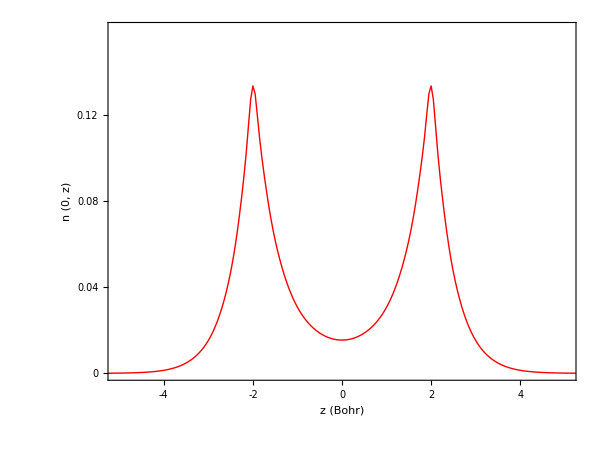

```mathematica
Len=Length[cubedata[[1]][[1]]]

ListP=Table[{zg[[i]],cubedata[[1]][[1]][[i]]},{i,Len}];


Xmin=-5.05;
Xmax=5.05;
Ymin=0;
Ymax=0.16;




LLP=ListLinePlot[ListP,
PlotRange->{{Xmin,Xmax},{Ymin,Ymax}},
PlotStyle->{Thick,Red,Solid}
];

Fntsx=20;


Show[{LLP},ImageSize->600,
AspectRatio->3/4,
(*FrameTicks->{{0,-1,1,-2,2,-3,3,4,-4,-5,5},{0,0.05,0.1,0.15,.2}},*)
FrameTicksStyle->Directive[Black,Fntsx],FrameStyle->Directive[Black,Thick],
BaseStyle->Directive[FontSize->Fntsx,FontFamily-> "Times"],
Frame->True,
FrameTicks->{{{0,0.04,0.08,0.12},None},{{-4,-2,0,2,4},None}},
FrameLabel-> {Style["z (Bohr)",{Bold,Fntsx,Black} ],Style["n (0, z)",{Bold,Black,Fntsx}]}]
```